```mathematica
f[x_,mu_,s_]:=1/Sqrt[2*Pi*s^2]Exp[-(x-mu)^2/2/s^2]
```

```mathematica
fs[x_,mu_,s_]:=Series[1/Sqrt[2*Pi*s^2]Exp[-(x-mu)^2/2/s^2],{mu,0,6}]
fs
```

General::ivar: 0.04 不是一个有效的变量.

General::stop: 在本次计算中，General::ivar 的进一步输出将被抑制.

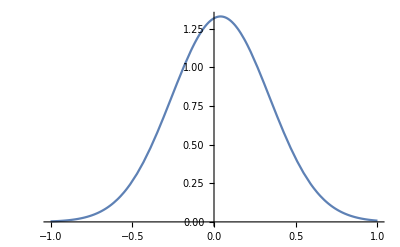

```mathematica
(* exp(-(x-0.04)^2/2/0.3^2 *)
Plot[{f[x,0.04,0.3],fs[x,0.04,0.3]},{x,-1,1},PlotLegends->"N(0.04,0.3)"]
```

```mathematica
a = 0;
st = -2;
ed = 2;
num = 20000;
dx = (ed - st)/num;
For[i=0,i<num,i++,a = a +(f[st+dx*i,0,0.3] + f[st+dx*(i+1),0,0.3])*dx/2];
Print[a];
Print[Integrate[f[x,0,0.3],{x,-2,2}]];
```

1.

1.

```mathematica
a
```

4999.34

```mathematica
Series[Exp[-(x-mu)^2/2/s^2],{mu,0,6}]
```

ⅇ^(-x^2/(2 s^2))+(ⅇ^(-x^2/(2 s^2)) x mu)/s^2-((ⅇ^(-x^2/(2 s^2)) (s^2-x^2)) mu^2)/(2 s^4)+1/3 ⅇ^(-x^2/(2 s^2)) (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)) mu^3+1/4 ⅇ^(-x^2/(2 s^2)) (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)) mu^4+1/5 ⅇ^(-x^2/(2 s^2)) (-(-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2))/(3 s^2)+(x (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)))/(4 s^2)) mu^5+1/6 ⅇ^(-x^2/(2 s^2)) (-(-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2))/(4 s^2)+(x (-(-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2))/(3 s^2)+(x (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)))/(4 s^2)))/(5 s^2)) mu^6+O[mu]^7

```mathematica
Simplify[CoefficientList[%149,mu]]
```

{ⅇ^(-x^2/(2 s^2)),(ⅇ^(-x^2/(2 s^2)) x)/s^2,(ⅇ^(-x^2/(2 s^2)) (-s^2+x^2))/(2 s^4),(ⅇ^(-x^2/(2 s^2)) (-3 s^2 x+x^3))/(6 s^6),(ⅇ^(-x^2/(2 s^2)) (3 s^4-6 s^2 x^2+x^4))/(24 s^8),(ⅇ^(-x^2/(2 s^2)) x (15 s^4-10 s^2 x^2+x^4))/(120 s^10),(ⅇ^(-x^2/(2 s^2)) (-15 s^6+45 s^4 x^2-15 s^2 x^4+x^6))/(720 s^12)}

```mathematica
fs[0,0.04,0.3]
```

General::ivar: 0.04 不是一个有效的变量.

Series[1.31804,{0.04,0,6}]